## About this program

Tested on the Mathematica version 14.3
Equation and Section numbers refer to the manuscript  (see README.md).

## Some preparatory definitions

```mathematica
(* Autosave after every execution *)
(*CurrentValue[$FrontEnd,"NotebookAutoSave"]=True*)
```

```mathematica
(* Do not use Sinh, Cosh https://mathematica.stackexchange.com/a/7800 *)
$PrePrint=#/. {Csch[z_]:>1/Defer@Sinh[z],Sech[z_]:>1/Defer@Cosh[z]}&;
```

```mathematica
(* Set up a directory for saving files *)
With[{dirname=FileNameJoin[{NotebookDirectory[],"data"}]},
Switch[FileType[dirname],
None,CreateDirectory[dirname] (*create dir*),
Directory,Null (*do nothing*),
File,Print["File with same name already exists!"] (*error!*)]];
(* Set the directory "/data" as a default directory *)
SetDirectory[FileNameJoin[{NotebookDirectory[],"data"}]]
```

C:\Users\ievle\Desktop\Current projects\Shifman - sphaleron\wolfram\data

## (Super)potentials

### Some routines

```mathematica
ComputePotential[W_]:=Module[{WX,WY},
WX=D[W,X]//Simplify;
WY=D[W,Y]//Simplify;
ans=1/2*(WX^2+WY^2)//FullSimplify
];

SolveForVacua[W_]:=Module[{WX,WY},
WX=D[W,X]//Simplify;
WY=D[W,Y]//Simplify;
Solve[{WX==0,WY==0},{X,Y}]
];
```

### Full superpotential (Sec. 3.2)

The fields ϕ_1,ϕ_2 from the paper are denoted here as X,Y respectively (for brevity of code)

```mathematica
W=m^2/(4*λ)*Υ-λ/3*Υ^3+1/2*m*κ*X*Υ/.{Υ->Sqrt[(X+1/2*m/λ*κ)^2+Y^2]};(*Superpotential*)
V=ComputePotential[W]//Simplify//Expand
DesiredPotential=(λ^2/2*(X^2+Y^2-m^2/(4*λ^2))^2+κ^2*m^2/8*Y^2)
Print["Next output should be zero (check V=|W'|^2):"]
V-DesiredPotential//Simplify
```

-1/4 m^2 X^2-(m^2 Y^2)/4+1/8 m^2 Y^2 κ^2+m^4/(32 λ^2)+(X^4 λ^2)/2+X^2 Y^2 λ^2+(Y^4 λ^2)/2

1/8 m^2 Y^2 κ^2+1/2 (X^2+Y^2-m^2/(4 λ^2))^2 λ^2

Next output should be zero (check V=|W'|^2):

0

```mathematica
(* Can also rewrite the potential in a different form *)
Vcomplex=λ^2/2*Abs[(X+I*Y)^2-m^2/(4*λ^2)]^2+(κ^2/8-1/2)*m^2*Y^2
Print["Next output should be zero (compare two forms of V):"]
(Vcomplex//ComplexExpand)-DesiredPotential//Simplify
```

m^2 Y^2 (-1/2+κ^2/8)+1/2 λ^2 Abs[(X+ⅈ Y)^2-m^2/(4 λ^2)]^2

Next output should be zero (compare two forms of V):

0

```mathematica
(* Save the expressions for the (super)potentials to files *)
Export["W.json",W, "ExpressionJSON"];
Export["V.json",V, "ExpressionJSON"];
```

### Behaviour near the singularity

```mathematica
Wsing=W/.{X->-κ*m/(2*λ)+Υ*Cos[θ],Y->Υ*Sin[θ]};
Simplify[Series[Wsing,{Υ,0,3}],Assumptions->{Υ>0,m>0,-1<κ<1}]
```

-((m^2 (-1+κ^2)) Υ)/(4 λ)+1/2 m κ Cos[θ] Υ^2-(λ Υ^3)/3+O[Υ]^4

## Mass matrix on the field space

### Build the mass matrix

```mathematica
fields={X,Y};
FermMass=Table[Table[D[W,f1,f2]//Simplify,{f1,fields}],{f2,fields}];
```

```mathematica
(* Save to file *)
Export["FermMass.json",FermMass, "ExpressionJSON"];
```

### At the (classical) vacua

```mathematica
sub=SolveForVacua[W]
Simplify[FermMass/.sub[[1]],Assumptions->{-1<κ<1,m>0,λ>0}]//MatrixForm
Simplify[FermMass/.sub[[2]],Assumptions->{-1<κ<1,m>0,λ>0}]//MatrixForm
```

{{X→-m/(2 λ),Y→0},{X→m/(2 λ),Y→0}}

(-m | 0
0 | (m κ)/2)

(-m | 0
0 | -(m κ)/2)

### In the quasiclassical limit λ->0, generic κ (Cartesian)

```mathematica
FermMassQCseries=Simplify[Series[FermMass,{λ,0,1}],Assumptions->{λ>0,κ>0,m>0}];
FermMassQCseries//MatrixForm
```

(-2 X λ+O[λ]^2 | -(Y λ)/κ^2+O[λ]^2
-(Y λ)/κ^2+O[λ]^2 | -(m (-1+κ^2))/(2 κ)-(X λ)/κ^2+O[λ]^2)

```mathematica
FermMassQC=Normal[FermMassQCseries];
FermMassQC//MatrixForm
EigsysQC=Simplify[Series[Eigensystem[FermMassQC],{λ,0,1}],Assumptions->{λ>0,1>κ>0,m>0}];

Print["First eigenvalue and eigenvector:"]
EigsysQC[[1]][[1]]
Simplify[EigsysQC[[2]][[1]]*(2*Y*λ)]

Print["Second eigenvalue and eigenvector:"]
EigsysQC[[1]][[2]]
Simplify[EigsysQC[[2]][[2]]*(-m*κ*(1-κ^2))]
```

(-2 X λ | -(Y λ)/κ^2
-(Y λ)/κ^2 | -(m (-1+κ^2))/(2 κ)-(X λ)/κ^2)

First eigenvalue and eigenvector:

-2 X λ+O[λ]^2

{-m κ (-1+κ^2)+2 X (-1+2 κ^2) λ+(4 Y^2 λ^2)/(m κ-m κ^3)+O[λ]^3,2 Y λ}

Second eigenvalue and eigenvector:

-(m (-1+κ^2))/(2 κ)-(X λ)/κ^2+O[λ]^2

{2 Y λ+O[λ]^2,m κ (-1+κ^2)}

### In the quasiclassical limit λ->0, generic κ (polar, close to the singularity)

```mathematica
FermMassQCseries=Simplify[Series[FermMass/.{X->-κ*m/(2*λ)+Υ*Cos[θ],Y->Υ*Sin[θ]},{λ,0,1}],Assumptions->{λ>0,-1<κ<1,m>0,Υ>0}];
FermMassQCseries//MatrixForm
```

(-(m^2 (-1+κ^2) Sin[θ]^2)/(4 Υ λ)-1/4 m κ Cos[θ] (-5+Cos[2 θ])-1/2 (Υ (3+Cos[2 θ])) λ+O[λ]^2 | (m^2 (-1+κ^2) Sin[2 θ])/(8 Υ λ)+1/2 m κ Sin[θ]^3-Υ Cos[θ] Sin[θ] λ+O[λ]^2
(m^2 (-1+κ^2) Sin[2 θ])/(8 Υ λ)+1/2 m κ Sin[θ]^3-Υ Cos[θ] Sin[θ] λ+O[λ]^2 | -(m^2 (-1+κ^2) Cos[θ]^2)/(4 Υ λ)+1/2 m κ Cos[θ]^3+1/2 Υ (-3+Cos[2 θ]) λ+O[λ]^2)

```mathematica
FermMassQC=Normal[FermMassQCseries];
FermMassQC//MatrixForm
EigsysQC=Simplify[Series[Eigensystem[FermMassQC],{λ,0,0}],Assumptions->{λ>0,-1<κ<1,m>0}];

Print["First eigenvalue and eigenvector:"]
EigsysQC[[1]][[1]]
Simplify[EigsysQC[[2]][[1]]*Sin[θ]]

Print["Second eigenvalue and eigenvector:"]
EigsysQC[[1]][[2]]
Simplify[EigsysQC[[2]][[2]]*Cos[θ]]
```

(-1/4 m κ Cos[θ] (-5+Cos[2 θ])-1/2 λ Υ (3+Cos[2 θ])-(m^2 (-1+κ^2) Sin[θ]^2)/(4 λ Υ) | -λ Υ Cos[θ] Sin[θ]+1/2 m κ Sin[θ]^3+(m^2 (-1+κ^2) Sin[2 θ])/(8 λ Υ)
-λ Υ Cos[θ] Sin[θ]+1/2 m κ Sin[θ]^3+(m^2 (-1+κ^2) Sin[2 θ])/(8 λ Υ) | -(m^2 (-1+κ^2) Cos[θ]^2)/(4 λ Υ)+1/2 m κ Cos[θ]^3+1/2 λ Υ (-3+Cos[2 θ]))

First eigenvalue and eigenvector:

m κ Cos[θ]+O[λ]^1

{Cos[θ]+O[λ]^1,Sin[θ]}

Second eigenvalue and eigenvector:

-(m^2 (-1+κ^2))/(4 Υ λ)+1/2 m κ Cos[θ]+O[λ]^1

{-Sin[θ]+O[λ]^1,Cos[θ]}

### In the limit κ->0

```mathematica
FermMassQCseries=Simplify[Series[FermMass/.{X->-κ*m/(2*λ)+Υ*Cos[θ],Y->Υ*Sin[θ]},{κ,0,1}],Assumptions->{Υ>0,λ>0,-1<κ<1,m>0}];
FermMassQCseries//MatrixForm
```

((-(3 λ Υ)/2-1/2 λ Υ Cos[2 θ]+(m^2 Sin[θ]^2)/(4 λ Υ))-1/8 (m (-9 Cos[θ]+Cos[3 θ])) κ+O[κ]^2 | -((m^2+4 λ^2 Υ^2) Sin[2 θ])/(8 (λ Υ))+1/2 m Sin[θ]^3 κ+O[κ]^2
-((m^2+4 λ^2 Υ^2) Sin[2 θ])/(8 (λ Υ))+1/2 m Sin[θ]^3 κ+O[κ]^2 | ((m^2 Cos[θ]^2)/(4 λ Υ)+1/2 λ Υ (-3+Cos[2 θ]))+1/2 m Cos[θ]^3 κ+O[κ]^2)

```mathematica
FermMassQC=Normal[FermMassQCseries];
FermMassQC//MatrixForm
EigsysQC=Simplify[Series[Eigensystem[FermMassQC],{κ,0,1}],Assumptions->{Υ>0,λ>0,-1<κ<1,m>0}];

Print["First eigenvalue and eigenvector:"]
EigsysQC[[1]][[1]]
Simplify[EigsysQC[[2]][[1]]]

Print["Second eigenvalue and eigenvector:"]
EigsysQC[[1]][[2]]
Simplify[EigsysQC[[2]][[2]]]
```

(-(3 λ Υ)/2-1/2 λ Υ Cos[2 θ]-1/8 m κ (-9 Cos[θ]+Cos[3 θ])+(m^2 Sin[θ]^2)/(4 λ Υ) | 1/2 m κ Sin[θ]^3-((m^2+4 λ^2 Υ^2) Sin[2 θ])/(8 λ Υ)
1/2 m κ Sin[θ]^3-((m^2+4 λ^2 Υ^2) Sin[2 θ])/(8 λ Υ) | (m^2 Cos[θ]^2)/(4 λ Υ)+1/2 m κ Cos[θ]^3+1/2 λ Υ (-3+Cos[2 θ]))

First eigenvalue and eigenvector:

-2 (λ Υ)+m Cos[θ] κ+O[κ]^2

{Cot[θ]-(2 (m λ Υ Csc[θ]) κ)/(m^2+4 λ^2 Υ^2)+O[κ]^2,1}

Second eigenvalue and eigenvector:

(m^2/(4 λ Υ)-λ Υ)+1/2 m Cos[θ] κ+O[κ]^2

{-Tan[θ]-(2 (m λ Υ Sec[θ] Tan[θ]) κ)/(m^2+4 λ^2 Υ^2)+O[κ]^2,1}

## Degenerate kinks (Sec. 3.3)

### Kink and sphaleron energy

```mathematica
(* Computation through the superpotential. Checked below by direct integration. *)
ClassicVEV=SolveForVacua[W]
WvacMinus=FullSimplify[W/.ClassicVEV[[1]],Assumptions->{λ>0,m>0,Element[κ,Reals]}]//Factor
WvacPlus=FullSimplify[W/.ClassicVEV[[2]],Assumptions->{λ>0,m>0,Element[κ,Reals]}]//Factor
Ekink=FullSimplify[WvacPlus-WvacMinus,Assumptions->{-1<κ<1}]
Esph=FullSimplify[WvacPlus+WvacMinus,Assumptions->{-1<κ<1}]
```

{{X→-m/(2 λ),Y→0},{X→m/(2 λ),Y→0}}

-(m^3 (-1+κ) (2+κ) Abs[-1+κ])/(24 λ^2)

-(m^3 (-2+κ) (1+κ) Abs[1+κ])/(24 λ^2)

-(m^3 κ (-3+κ^2))/(12 λ^2)

m^3/(6 λ^2)

### Kink profiles (bosonic)

```mathematica
(* Kink profiles *)
XtrajKink=m/(2*λ)*Tanh[κ*m*z/2];
YtrajKink=m/(2*λ)*Sqrt[1-κ^2]*1/Cosh[κ*m*z/2];
KinkSub={X->XtrajKink,Y->YtrajKink};

(* Check Bogomolny equations *)
WX=Simplify[D[W,X]/.KinkSub,Assumptions->{-1<κ<1,λ>0,m>0,Element[z,Reals]}];
WY=Simplify[D[W,Y]/.KinkSub,Assumptions->{-1<κ<1,λ>0,m>0,Element[z,Reals]}];
Print["Next two outputs should be zero (Bogomolny equations):"]
Simplify[D[XtrajKink,z]-WX,Assumptions->{-1<κ<1,λ>0,m>0,Element[z,Reals]}]
Simplify[D[YtrajKink,z]-WY,Assumptions->{-1<κ<1,λ>0,m>0,Element[z,Reals]}]
```

Next two outputs should be zero (Bogomolny equations):

0

0

### Zero modes

```mathematica
(* Bosonic zero modes are proportional to derivative of the kink trajectory *)
ConvenientPrefactor=4*λ/(m^2*κ);
zeroXbos=ConvenientPrefactor*Simplify[D[XtrajKink,z]]
zeroYbos=ConvenientPrefactor*Simplify[D[YtrajKink,z]]
```

1/Cosh[(m z κ)/2]^2

-(4 √(1-κ^2) Sinh[(m z κ)/2]^3)/Sinh[m z κ]^2

```mathematica
(* Fermionic zero modes are generated by SUSY transformations, which are proportional to W' *)
WX=Simplify[D[W,X]/.KinkSub,Assumptions->{-1<κ<1,m>0,λ>0,Element[z,Reals]}];
WY=FullSimplify[D[W,Y]/.KinkSub,Assumptions->{-1<κ<1,m>0,λ>0,Element[z,Reals]}];

ConvenientPrefactor=4*λ/(m^2*κ);
zeroXferm=ConvenientPrefactor*WX
zeroYferm=ConvenientPrefactor*WY
```

1/Cosh[(m z κ)/2]^2

-(4 √(1-κ^2) Sinh[(m z κ)/2]^3)/Sinh[m z κ]^2

```mathematica
(* Check SUSY *)
Print["The following two outputs should be zero (SUSY):"]
zeroXbos-zeroXferm//Simplify
zeroYbos-zeroYferm//Simplify
```

The following two outputs should be zero (SUSY):

0

0

### Fermion mass on kink background (κ-notation)

```mathematica
FermMassOnKink=Simplify[FermMass/.KinkSub,Assumptions->{-1<κ<1,m>0,λ>0}];
FermMassOnKink//MatrixForm
```

(-(m^2 (κ-κ^3+2 κ Cosh[m z κ]+(1+κ^2) Sinh[m z κ]) Tanh[(m z κ)/2])/(2 Cosh[(m z κ)/2]^2 (1+κ Tanh[(m z κ)/2]) √((m+m κ Tanh[(m z κ)/2])^2)) | -(m^2 (κ Cosh[m z κ]+Sinh[m z κ]))/(2 Cosh[(m z κ)/2]^3 (1+κ Tanh[(m z κ)/2]) √(-(m+m κ Tanh[(m z κ)/2])^2/(-1+κ^2)))
-(m^2 (κ Cosh[m z κ]+Sinh[m z κ]))/(2 Cosh[(m z κ)/2]^3 (1+κ Tanh[(m z κ)/2]) √(-(m+m κ Tanh[(m z κ)/2])^2/(-1+κ^2))) | -(m^2 (8-15 κ^2+7 κ^4-4 (-2+κ^2+2 κ^4) Cosh[m z κ]+κ^2 (3+κ^2) Cosh[2 m z κ]+14 κ Sinh[m z κ]-18 κ^3 Sinh[m z κ]+κ Sinh[2 m z κ]+3 κ^3 Sinh[2 m z κ]))/(16 Cosh[(m z κ)/2]^4 (1+κ Tanh[(m z κ)/2])^2 √((m+m κ Tanh[(m z κ)/2])^2)))

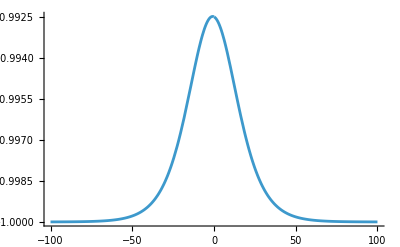

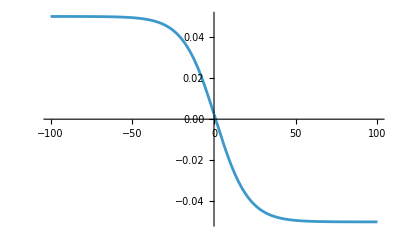

```mathematica
MassEigOnKink=Eigenvalues[FermMassOnKink];
temp=Simplify[MassEigOnKink/.{m->1,λ->1,κ->0.1}];

(* Note: one of the eigenvalues passes through zero and changes sign. This gives rise to a fermionic zero mode. *)
Plot[temp[[1]],{z,-100,100}]
Plot[temp[[2]],{z,-100,100}]
```

### Fermions on kink background (α-notation from Sec. 3.6.1)

```mathematica
FermMassα=FermMass/.{κ->Sqrt[1-α^2]};(* Mass matrix *)
```

```mathematica
(* Kink profiles *)
XtrajKinkα=m/(2*λ)*Tanh[Sqrt[1-α^2]*m*z/2];
YtrajKinkα=m/(2*λ)*α*1/Cosh[Sqrt[1-α^2]*m*z/2];
SubKinkα={X->XtrajKinkα,Y->YtrajKinkα};
FermMassKink=Simplify[FermMassα/.SubKinkα,Assumptions->{-1<α<1,m>0,λ>0}];
FermMassKink//MatrixForm
```

((m (-3 α^2 √(1-α^2) Cosh[1/2 m z √(1-α^2)]+√(1-α^2) (-4+α^2) Cosh[3/2 m z √(1-α^2)]+2 (-2+α^4+(-4+3 α^2) Cosh[m z √(1-α^2)]) Sinh[1/2 m z √(1-α^2)]) Tanh[1/2 m z √(1-α^2)])/(4 Cosh[1/2 m z √(1-α^2)]^3 (1-α^2+α^2/(Cosh[1/2 m z √(1-α^2)]^2)+2 √(1-α^2) Tanh[1/2 m z √(1-α^2)]+Tanh[1/2 m z √(1-α^2)]^2)^(3/2)) | -(m α (2 √(1-α^2) Cosh[3/2 m z √(1-α^2)]+2 (1-(-2+α^2) Cosh[m z √(1-α^2)]) Sinh[1/2 m z √(1-α^2)]))/(4 Cosh[1/2 m z √(1-α^2)]^4 (1-α^2+α^2/(Cosh[1/2 m z √(1-α^2)]^2)+2 √(1-α^2) Tanh[1/2 m z √(1-α^2)]+Tanh[1/2 m z √(1-α^2)]^2)^(3/2))
-(m α (2 √(1-α^2) Cosh[3/2 m z √(1-α^2)]+2 (1-(-2+α^2) Cosh[m z √(1-α^2)]) Sinh[1/2 m z √(1-α^2)]))/(4 Cosh[1/2 m z √(1-α^2)]^4 (1-α^2+α^2/(Cosh[1/2 m z √(1-α^2)]^2)+2 √(1-α^2) Tanh[1/2 m z √(1-α^2)]+Tanh[1/2 m z √(1-α^2)]^2)^(3/2)) | (m (-α^2-7 α^4+4 (1-5 α^2+2 α^4) Cosh[m z √(1-α^2)]-(4-5 α^2+α^4) Cosh[2 m z √(1-α^2)]+4 √(1-α^2) Sinh[m z √(1-α^2)]-18 α^2 √(1-α^2) Sinh[m z √(1-α^2)]-4 √(1-α^2) Sinh[2 m z √(1-α^2)]+3 α^2 √(1-α^2) Sinh[2 m z √(1-α^2)]))/(16 Cosh[1/2 m z √(1-α^2)]^4 (1-α^2+α^2/(Cosh[1/2 m z √(1-α^2)]^2)+2 √(1-α^2) Tanh[1/2 m z √(1-α^2)]+Tanh[1/2 m z √(1-α^2)]^2)^(3/2)))

#### Zero mode

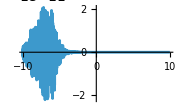

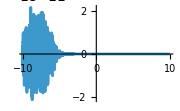

```mathematica
(* Check that the exact zero mode indeed satisfies the Dirac equation. Mathematica can do it analytically, but it takes a long time, so here I am checking this numerically. *)
ψ={{D[XtrajKinkα,z]},{D[YtrajKinkα,z]}}/.{m->1,λ->1}; (*omitting the spinor index*)
Mψ=Simplify[Dot[FermMassKink/.{m->1,λ->1},ψ],Assumptions->{-1<α<1,Element[z,Reals]}];
dψ=D[ψ,z]//Simplify;
DirEq=dψ-Mψ;(* Dirac equation, static case *)
Plot[DirEq[[1]]/.{α->0.1},{z,-10,10},ImageSize->Small,PlotRange->All]
Plot[DirEq[[2]]/.{α->0.1},{z,-10,10},ImageSize->Small,PlotRange->All]
(* Within the numerical error, the plots give zero *)
```

#### Attempt on finding the first non - zero mode (“transversal shift”) to O(α)

```mathematica
(* Mass matrix to O(α) *)
temp=Series[FermMassKink/.{m->1,λ->1},{α,0,1}]//Normal;
FermMassKinkApprox=Simplify[temp,Assumptions->{Element[z,Reals]}];
FermMassKinkApprox//MatrixForm
```

(-Tanh[z/2] | -α/(2 Cosh[z/2])
-α/(2 Cosh[z/2]) | -1/2 Tanh[z/2])

```mathematica
(* Solve homogenious Dirac equation *)
DSolve[y'[x]+Tanh[x/2]*y[x]+1/(2*Cosh[x/2]^2)==0,y[x],x]
```

{{y[x]→-x/(2 Cosh[x/2]^2)+C[1]/Cosh[x/2]^2}}

```mathematica
(* Write down the mode and substitute into the Dirac equation *)
ψ={{-α*z/(2*Cosh[z/2]^2)},{1/Cosh[z/2]}};
ψ//MatrixForm
dψ=D[ψ,z]//Simplify;
Mψ=Dot[FermMassKinkApprox,ψ]//Simplify;
DirEq=dψ-Mψ//Simplify;
DirEq//MatrixForm(*Equation is satisfied to to O(α), so the eigenvalue is not captured at this order*)
```

(-(z α)/(2 Cosh[z/2]^2)
1/Cosh[z/2])

(0
-(z α^2)/(4 Cosh[z/2]^3))

## Sphaleron (Sec. 3.4)

### Sphaleron profile

```mathematica
XtrajSphaleron=m/(2*λ)*Tanh[m/2*z];
YtrajSphaleron=0;
SubSph={X->XtrajSphaleron,Y->YtrajSphaleron};

WX=Simplify[D[W,X]/.SubSph,Assumptions->{m>0,λ>0,Element[κ,Reals]}];

(* Let's plug into BPS equation and see what happens *)
Simplify[D[XtrajSphaleron,z]-WX,Assumptions->{m>0,λ>0,Element[κ,Reals]}]
(* BPS equations is satisfied at least piecewise *)
Simplify[D[XtrajSphaleron,z]-WX,Assumptions->{m>0,λ>0,κ>0,z>0}]
```

(m^2 (-κ-Tanh[(m z)/2]+√((κ+Tanh[(m z)/2])^2)))/(4 λ Cosh[(m z)/2]^2 √((κ+Tanh[(m z)/2])^2))

0

### Fermion mass on sphaleron background

```mathematica
FermMassSph=Simplify[FermMass/.SubSph,Assumptions->{m>0,λ>0,Element[z,Reals],,Element[κ,Reals]}];
FermMassSph//MatrixForm
```

(-(m Tanh[(m z)/2] (κ+Tanh[(m z)/2]))/Abs[κ+Tanh[(m z)/2]] | 0
0 | -(m (-1+κ^2+κ Tanh[(m z)/2]+Tanh[(m z)/2]^2))/(2 Abs[κ+Tanh[(m z)/2]]))

### Zero mode

```mathematica
(* Check the Dirac equation for the "translational" zero mode. It's has the same functional form as the bosonic mode. *)
ψsph=D[XtrajSphaleron,z]//Simplify

(* Piecewise solution *)
Print["The following two outputs should be zero (Dirac eq.):"]
Simplify[-D[ψsph,z]/ψsph-FermMassSph[[1]][[1]],Assumptions->{Tanh[m*z/2]<-κ}] (* D^\dagger ψ=0 *)
Simplify[+D[ψsph,z]/ψsph-FermMassSph[[1]][[1]],Assumptions->{Tanh[m*z/2]>-κ}](* D ψ=0 *)
```

m^2/(4 λ Cosh[(m z)/2]^2)

The following two outputs should be zero (Dirac eq.):

0

0

### Negative "transversal" mode

#### Negative bosonic mode

```mathematica
(* Bosonic fluctuation operator *)
fields={X,Y};
ddU=Table[Table[D[V,f1,f2]/.SubSph//Simplify,{f1,fields}],{f2,fields}];
ddU//MatrixForm
```

(1/2 m^2 (-1+3 Tanh[(m z)/2]^2) | 0
0 | (m^2 (-4+κ^2+κ^2 Cosh[m z]))/(8 Cosh[(m z)/2]^2))

```mathematica
SphNegModeBos=1/Cosh[m*z/2] (* Explicit answer for the mode  *)
SphNegModeEigenvalue=-(D[SphNegModeBos,{z,2}]-ddU[[2]][[2]]*SphNegModeBos)/SphNegModeBos//Simplify (* This will give the eigenvalue *)
```

1/Cosh[(m z)/2]

1/4 m^2 (-1+κ^2)

#### At -1<κ< 1 it' s a would-be negative fermionic mode, Sec. 3.4.4

```mathematica
(* Let's consider more closely the case Tanh[m*z/2]<-κ *)
AssumeHere={-1<κ<1,m>0,Element[z,Reals],Tanh[m*z/2]<-κ};

(* Generate this mode by SUSY *)
M=Simplify[FermMassSph[[2]][[2]],Assumptions->AssumeHere];
(* This part is regular in z *)
ψ1zneg=Simplify[-Cos[ω*t]*SphNegModeBos,Assumptions->AssumeHere]
(* This part has a bad singularity in z and is non-normalizable *)
ψ2zneg=Simplify[1/ω*Sin[ω*t]*(-D[SphNegModeBos,z]-M*SphNegModeBos),Assumptions->AssumeHere]

(* Frequency is real at |κ|>1, imaginary at |κ|<1 *)
ωVal=Simplify[Sqrt[SphNegModeEigenvalue] ,Assumptions->AssumeHere]
(* Check the Dirac equation *)
Print["The following two outputs should be zero (Dirac eq.):"]
Simplify[((-D[ψ1zneg,z]-M*ψ1zneg)+D[ψ2zneg,t])/.{ω->ωVal},Assumptions->AssumeHere]
Simplify[(-D[ψ1zneg,t]+(D[ψ2zneg,z]-M*ψ2zneg))/.{ω->ωVal},Assumptions->AssumeHere]
```

-Cos[t ω]/Cosh[(m z)/2]

-(m (-1+κ^2) Sin[t ω])/(2 ω Cosh[(m z)/2] (κ+Tanh[(m z)/2]))

1/2 m √(-1+κ^2)

The following two outputs should be zero (Dirac eq.):

0

0

```mathematica
(* Let's consider more closely the case Tanh[m*z/2]>-κ *)
AssumeHere={-1<κ<1,m>0,Element[z,Reals],Tanh[m*z/2]>-κ};

(* Generate this mode by SUSY *)
M=Simplify[FermMassSph[[2]][[2]],Assumptions->AssumeHere];
(* This part is regular in z *)
ψ1zpos=Simplify[1/ω*Sin[ω*t]*(D[SphNegModeBos,z]-M*SphNegModeBos),Assumptions->AssumeHere]
(* This part has a bad singularity in z and is non-normalizable *)
ψ2zpos=Simplify[Cos[ω*t]*SphNegModeBos,Assumptions->AssumeHere]

(* Frequency is real at |κ|>1, imaginary at |κ|<1 *)
ωVal=Simplify[Sqrt[SphNegModeEigenvalue] ,Assumptions->AssumeHere]
(* Check the Dirac equation *)
Print["The following two outputs should be zero (Dirac eq.):"]
Simplify[((-D[ψ1zpos,z]-M*ψ1zpos)+D[ψ2zpos,t])/.{ω->ωVal},Assumptions->AssumeHere]
Simplify[(-D[ψ1zpos,t]+(D[ψ2zpos,z]-M*ψ2zpos))/.{ω->ωVal},Assumptions->AssumeHere]
```

(m (-1+κ^2) Sin[t ω])/(2 ω Cosh[(m z)/2] (κ+Tanh[(m z)/2]))

Cos[t ω]/Cosh[(m z)/2]

1/2 m √(-1+κ^2)

The following two outputs should be zero (Dirac eq.):

0

0

```mathematica
(* Let's compare the spinor components in the two subregions of z *)
```

```mathematica
ψ1zneg+ψ2zpos//Simplify
ψ2zneg+ψ1zpos//Simplify
```

0

0

#### At κ = 1 it becomes a zero mode

```mathematica
(* Check the Dirac equation *)
M=Simplify[FermMassSph[[2]][[2]]/.{κ->1},Assumptions->{m>0,Element[z,Reals]}]
ψsph=1/Cosh[m*z/2]
Print["The following output should be zero (Dirac eq.):"]
Simplify[D[ψsph,z]/ψsph-M]
```

-1/2 m Tanh[(m z)/2]

1/Cosh[(m z)/2]

The following output should be zero (Dirac eq.):

0

## Effective worldline description

### Bosonic part (Sec. 3.6.1)

```mathematica
(* Ansatz *)
AnsatzX=m/(2*λ)*Tanh[κ1*m*z/2];
AnsatzY=m/(2*λ)*Sqrt[1-κ1^2]*1/Cosh[κ1*m*z/2];

(* Substitute into the action *)
dX2=D[AnsatzX,z]^2;
dY2=D[AnsatzY,z]^2;
AnsatzIntegrand=dX2/2+dY2/2+(V/.{X->AnsatzX,Y->AnsatzY})//Simplify
```

-(m^4 (κ^2 (-1+κ1^2)-κ1^2 (1+3 κ1^2)+(-1+κ1^2) (κ^2+κ1^2) Cosh[m z κ1]))/(64 λ^2 Cosh[(m z κ1)/2]^4)

```mathematica
AnsatzAction=Integrate[AnsatzIntegrand,{z,-Infinity,Infinity},Assumptions->{m>0,0<κ<1,0<κ1<1,λ>0}]
```

(m^3 (-3 κ^2 (-1+κ1^2)+κ1^2 (3+κ1^2)))/(24 κ1 λ^2)

```mathematica
(* This gives the potential after discarding the  term *)
AnsatzActionβ=AnsatzAction/.{κ->Sqrt[1-α^2],κ1->Sqrt[1-β^2]};
Series[AnsatzActionβ,{β,0,4}]
```

m^3/(6 λ^2)-((m^3 α^2) β^2)/(8 λ^2)-((m^3 (-1+α^2)) β^4)/(16 λ^2)+O[β]^5

```mathematica
Series[AnsatzActionβ,{β,0,4}]//Normal//InputForm
```

m^3/(6*λ^2) - (m^3*α^2*β^2)/(8*λ^2) - 
 (m^3*(-1 + α^2)*β^4)/(16*λ^2)

```mathematica
Veffqm=m^3/(6*λ^2) - (m^3*α^2*β^2)/(8*λ^2) - 
 (m^3*(-1 )*β^4)/(16*λ^2)
(* Check kink mass *)
Veffqm/.{β->α}
Series[Ekink/.{κ->Sqrt[1-α^2]},{α,0,5}]
```

m^3/(6 λ^2)-(m^3 α^2 β^2)/(8 λ^2)+(m^3 β^4)/(16 λ^2)

m^3/(6 λ^2)-(m^3 α^4)/(16 λ^2)

m^3/(6 λ^2)-(m^3 α^4)/(16 λ^2)+O[α]^6

```mathematica
(* Now let's derive the kinetic term *)

(* This is contribution from the  *)
βkinXintegrand=1/2*(D[AnsatzX/.κ1->Sqrt[1-β^2],β]^2//Simplify)/.β->0
βkinX=Integrate[βkinXintegrand,{z,-Infinity,Infinity},Assumptions->{m>0,λ>0,0<κ<1}]

(* This is contribution from the  *)
βkinYintegrand=1/2*(D[AnsatzY/.κ1->Sqrt[1-β^2],β]^2//Simplify)/.β->0
βkinY=Integrate[βkinYintegrand,{z,-Infinity,Infinity},Assumptions->{m>0,λ>0,0<κ<1}]
```

0

0

m^2/(8 λ^2 Cosh[(m z)/2]^2)

m/(2 λ^2)

## One - parameter family of N=1 supersymmetrizations of ϕ^4 (Appendix A)

### The superpotential

```mathematica
DesiredPotentialphi4=λ^2/2*(X^2-m^2/(4*λ^2))^2
Wphi4=m^2/(4*λ)*Υ-λ/3*Υ^3+λ*κ*X*Υ/.{Υ->Sqrt[(X+κ)^2]}

Wphi4X=D[Wphi4,X];
Simplify[DesiredPotentialphi4-1/2*Wphi4X^2,Assumptions->{λ>0,m>0,Element[X,Reals],Element[κ,Reals]}]
```

1/2 (X^2-m^2/(4 λ^2))^2 λ^2

(m^2 √((X+κ)^2))/(4 λ)+X κ √((X+κ)^2) λ-1/3 ((X+κ)^2)^(3/2) λ

0

```mathematica
(* Simplify assuming κ very large and positive *)
Wphi4pos=Simplify[Wphi4,Assumptions->{λ>0,m>0,Element[X,Reals],Element[κ,Reals],κ+X>0}]//Expand

(* Simplify assuming κ very large and negative *)
Wphi4neg=Simplify[Wphi4,Assumptions->{λ>0,m>0,Element[X,Reals],Element[κ,Reals],κ+X<0}]//Expand
Wphi4pos+Wphi4neg
```

(m^2 X)/(4 λ)+(m^2 κ)/(4 λ)-(X^3 λ)/3-(κ^3 λ)/3

-(m^2 X)/(4 λ)-(m^2 κ)/(4 λ)+(X^3 λ)/3+(κ^3 λ)/3

0

```mathematica
(* The first derivative is discontinuous at X=-κ *)
D[Wphi4pos,X]/.{X->-κ}
D[Wphi4neg,X]/.{X->-κ}
```

m^2/(4 λ)-κ^2 λ

-m^2/(4 λ)+κ^2 λ

```mathematica
Wphi4simple=Wphi4/(m^3/(8*λ^2))/.{X->m/(2*λ)*x}
Simplify[Wphi4simple,Assumptions->{λ>0,m>0,Element[x,Reals],Element[κ,Reals],κ+m/(2*λ)*x>0}]//Expand
```

(8 λ^2 (1/2 m x κ √((κ+(m x)/(2 λ))^2)+(m^2 √((κ+(m x)/(2 λ))^2))/(4 λ)-1/3 ((κ+(m x)/(2 λ))^2)^(3/2) λ))/m^3

x-x^3/3+(2 κ λ)/m-(8 κ^3 λ^3)/(3 m^3)

### Plot a couple of examples

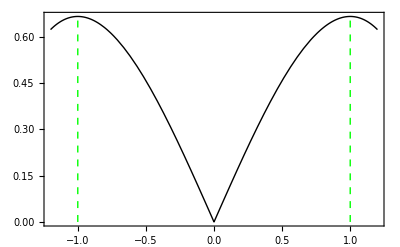

phi4_W_kappa0.pdf

```mathematica
Wforplot=Simplify[Wphi4simple/.{κ->0},Assumptions->{λ>0,m>0,Element[x,Reals]}];
maxy=Wforplot/.{x->+1};
lineStyle={Green,Dashed};
line1=Line[{{-1,0},{-1,maxy}}];
line2=Line[{{+1,0},{+1,maxy}}];

MyPlot=Plot[{Wforplot},{x,-1.2,1.2},
PlotStyle->{Thick,Black},Axes->False,Frame->True,FrameLabel->{"",""},
PlotRange->All,
LabelStyle->{Black,13},
Epilog->{Directive[lineStyle],line1,line2}
]

Export["phi4_W_kappa0.pdf",MyPlot]
```

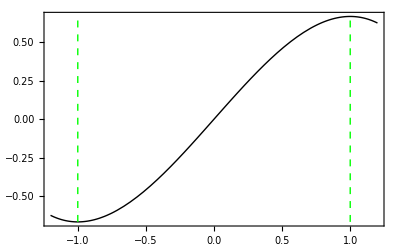

phi4_W_kappa10.pdf

```mathematica
κVal=10;
temp=Wphi4simple/.{κ->κVal};
Wforplot=Simplify[temp-(temp/.{x->0}),Assumptions->{λ>0,m>0,Element[x,Reals],κVal+m/(2*λ)*x>0}];

miny=Wforplot/.{x->-1};
maxy=Wforplot/.{x->+1};
lineStyle={Green,Dashed};
line1=Line[{{-1,miny},{-1,maxy}}];
line2=Line[{{+1,miny},{+1,maxy}}];

MyPlot=Plot[{Wforplot},{x,-1.2,1.2},
PlotStyle->{Thick,Black},Axes->False,Frame->True,FrameLabel->{"",""},
PlotRange->All,
LabelStyle->{Black,13},
Epilog->{Directive[lineStyle],line1,line2}
]

Export["phi4_W_kappa10.pdf",MyPlot]
```

## Instanton action at small alpha via differentiation (Sec. 3.6.1)

```mathematica
YtrajKinkα=YtrajKink/.{κ->Sqrt[1-α^2]}//Simplify
```

(m √(α^2))/(2 λ Cosh[1/2 m z √(1-α^2)])

```mathematica
dSdαIntegrand=YtrajKinkα^2*(1-Tanh[α*m*t/(2*Sqrt[2])]^2)
dSdα=(-α*m^2/4)*Integrate[dSdαIntegrand,{z,-Infinity,Infinity},{t,-Infinity,Infinity},Assumptions->{0<α<1,m>0,λ>0}]
```

(m^2 α^2 (1-Tanh[(m t α)/(2 √2)]^2))/(4 λ^2 Cosh[1/2 m z √(1-α^2)]^2)

ConditionalExpression[-(√2 m^2 α^2)/(√(1-α^2) λ^2), ]

```mathematica
dSdα=Normal[dSdα]
dSdαExpanded=Series[dSdα,{α,0,4}]
```

-(√2 m^2 α^2)/(√(1-α^2) λ^2)

-(√2 m^2 α^2)/λ^2-(m^2 α^4)/(√2 λ^2)+O[α]^5

```mathematica
(* Integration of the expanded formula above is straightforward. To re-check, however, let's first integrate and then expand. *)
Sα=Integrate[dSdα,{α,0,Α},Assumptions->{0<Α<1}]/.{Α->α}
Simplify[Series[Sα,{α,0,5}],Assumptions->{α>0}]
```

(m^2 (α √(1-α^2)-ArcSin[α]))/(√2 λ^2)

-((√2 m^2) α^3)/(3 λ^2)-(m^2 α^5)/(5 (√2 λ^2))+O[α]^6

## Quantum corrections (Sec. 3.5)

### Perturbative anomaly in superpotential

```mathematica
(* Compute the correction *)
Wanom=1/(4*Pi)*(D[W,{X,2}]+D[W,{Y,2}])//Simplify
```

(-m^2 (-1+κ^2)-6 m X κ λ-12 (X^2+Y^2) λ^2)/(8 π √(4 X^2+4 Y^2+(m^2 κ^2)/λ^2+(4 m X κ)/λ) λ)

```mathematica
(* Check the representation *)
Wcheck=1/(4*Pi)*( 1/Υ*(  m^2/(4*λ)*(1+2*κ^2) + 3/2*κ*m*X  ) - 3*λ*Υ)
Wcheck=Wcheck/.{Υ->Sqrt[(X+1/2*m/λ*κ)^2+Y^2]};
Print["Next output should be zero (alt. representation of Wanom):"]
Wanom-Wcheck//Simplify
```

(((3 m X κ)/2+(m^2 (1+2 κ^2))/(4 λ))/Υ-3 λ Υ)/(4 π)

Next output should be zero (alt. representation of Wanom):

0

```mathematica
(* Save to file *)
Export["Wanom.json",Wanom, "ExpressionJSON"];
```

### Corrections via expansion in λ/m

```mathematica
(* Expand up to (λ/m)^(MyOrder) *)
MyOrder=1;
```

#### Correction to scalar VEVs

```mathematica
AssumeHere={m>0,λ>0,-1<κ<1};
(* Recall the classical result *)
ClassicVEV
XvevCl=X/.ClassicVEV[[1]];
```

{{X→-m/(2 λ),Y→0},{X→m/(2 λ),Y→0}}

```mathematica
(* Expand the full superpotential as a power series in λ/m *)
Wfull=W+Wanom;
temp=Wfull/.{X->XvevCl+x,Y->y};
serW=Simplify[Normal[Series[temp,{λ,0,MyOrder}]],Assumptions->AssumeHere];
serW=serW//Simplify

(* Check if the classical vacuum is still a vacuum (it is not) *)
D[serW,x]/.{x->0,y->0}
D[serW,y]/.{x->0,y->0}
```

1/24 ((3 m (-2-4 π x^2+κ+2 π y^2 κ))/π+(m^3 (-1+κ)^2 (2+κ))/λ^2+(4 x (-6 π y^2+3 (-2+κ)+2 π x^2 (-1+κ)) λ)/(π (-1+κ)))

((-2+κ) λ)/(2 π (-1+κ))

0

```mathematica
dWdx=Simplify[D[serW,x],Assumptions->AssumeHere]
dWdy=Simplify[D[serW,y],Assumptions->AssumeHere]
(* Check that y=0 in the quantum vacuum *)
ysub=Solve[dWdy==0,y]
Solve[dWdy==0,x]
```

-m x+((-2-2 π y^2+2 π x^2 (-1+κ)+κ) λ)/(2 π (-1+κ))

(m y κ)/2-(2 x y λ)/(-1+κ)

{{y→0}}

{{x→(m (-1+κ) κ)/(4 λ)}}

```mathematica
(* Find the correction to the VEV of X *)
dWdx=dWdx/.ysub[[1]]//Simplify
xsub=Simplify[Solve[dWdx==0,x],Assumptions->AssumeHere]
```

-m x+((-2+2 π x^2 (-1+κ)+κ) λ)/(2 π (-1+κ))

{{x→(m-(√(m^2 π (-1+κ)-2 (-2+κ) λ^2))/(√π √(-1+κ)))/(2 λ)},{x→(m √π √(-1+κ)+√(m^2 π (-1+κ)-2 (-2+κ) λ^2))/(2 √π √(-1+κ) λ)}}

```mathematica
(* Write down the corrected VEV of X *)
x1=x/.xsub[[1]];
ΔX=Simplify[Series[x1,{λ,0,MyOrder}],Assumptions->AssumeHere]//Normal
```

((2-κ) λ)/(2 m π-2 m π κ)

```mathematica
(* Check the new solution *)
Xvev=XvevCl+ΔX
Yvev=0
quantVEV={X->Xvev,Y->Yvev};

Print["Next two outputs should be zero or suppressed by powers of λ:"]
dWdX=D[Wfull,X]/.quantVEV;
Series[dWdX,{λ,0,MyOrder}]
dWdY=D[Wfull,Y]/.quantVEV//Simplify
```

-m/(2 λ)+((2-κ) λ)/(2 m π-2 m π κ)

0

Next two outputs should be zero or suppressed by powers of λ:

O[λ]^2

0

#### Correction to kink mass

```mathematica
(* First vacuum *)
quantVEV1={X->Xvev,Y->Yvev}
(* Second vacuum (by symmetry) *)
quantVEV2={X->-Xvev/.{κ->-κ},Y->-Yvev/.{κ->-κ}}//Simplify

(* Check both vacua again *)
Print["Next two outputs should be zero or suppressed by powers of λ:"]
Series[D[Wfull,X]/.quantVEV1,{λ,0,MyOrder}]
Series[D[Wfull,X]/.quantVEV2,{λ,0,MyOrder}]
```

{X→-m/(2 λ)+((2-κ) λ)/(2 m π-2 m π κ),Y→0}

{X→m/(2 λ)-((2+κ) λ)/(2 m π+2 m π κ),Y→0}

Next two outputs should be zero or suppressed by powers of λ:

O[λ]^2

O[λ]^2

```mathematica
(* Compute the value of corrected superpotential in the first vacuum *)
Wvac1quant=Wfull/.quantVEV1;
serWvac1quant=Simplify[Series[Wvac1quant,{λ,0,MyOrder}],Assumptions->{λ>0,m>0,Element[κ,Reals]}]

(* Compare with the classical result *)
Simplify[serWvac1quant-WvacMinus]
FullSimplify[serWvac1quant-WvacMinus,Assumptions->-1<κ<1]
```

-(m^3 (-2+κ+κ^2) Abs[-1+κ])/(24 λ^2)-(m (-2+κ) (-1+κ))/(8 (π Abs[-1+κ]))+O[λ]^2

-(m (-2+κ) (-1+κ))/(8 (π Abs[-1+κ]))+O[λ]^2

(m (-2+κ))/(8 π)+O[λ]^2

```mathematica
(* Compute the value of corrected superpotential in the second vacuum *)
Wvac2quant=Wfull/.quantVEV2;
serWvac2quant=Simplify[Series[Wvac2quant,{λ,0,MyOrder}],Assumptions->{λ>0,m>0,Element[κ,Reals]}]

(* Compare with the classical result *)
Simplify[serWvac2quant-WvacPlus]
FullSimplify[serWvac2quant-WvacPlus,Assumptions->-1<κ<1]
```

(m^3 (2+κ-κ^2) Abs[1+κ])/(24 λ^2)-(m (1+κ) (2+κ))/(8 (π Abs[1+κ]))+O[λ]^2

-(m (1+κ) (2+κ))/(8 (π Abs[1+κ]))+O[λ]^2

-(m (2+κ))/(8 π)+O[λ]^2

```mathematica
(* Compute the corrected kink mass *)
Ekinkquant=FullSimplify[Normal[-serWvac1quant+serWvac2quant],Assumptions->AssumeHere]
(* Compare with the classical result *)
Ekink
ΔE=Ekinkquant-Ekink//Simplify
```

1/12 m κ (-3/π-(m^2 (-3+κ^2))/λ^2)

-(m^3 κ (-3+κ^2))/(12 λ^2)

-(m κ)/(4 π)

```mathematica
(* See when the first correction overwhelms the leading term *)
Simplify[λ/.Solve[Ekink==-ΔE,λ],Assumptions->{0<κ<1}]
```

{m √(π-(π κ^2)/3),ⅈ m √(π/3) √(-3+κ^2)}

### Investigating nature of vacua analytically (assuming 0<κ<1, left vacuum)

#### Simplify expression for superpotential

```mathematica
Wfull
Vfull=ComputePotential[Wfull]
```

1/2 m X κ √(Y^2+(X+(m κ)/(2 λ))^2)+(m^2 √(Y^2+(X+(m κ)/(2 λ))^2))/(4 λ)-1/3 (Y^2+(X+(m κ)/(2 λ))^2)^(3/2) λ+(-m^2 (-1+κ^2)-6 m X κ λ-12 (X^2+Y^2) λ^2)/(8 π √(4 X^2+4 Y^2+(m^2 κ^2)/λ^2+(4 m X κ)/λ) λ)

(4 Y^2 λ^2 (m^4 π κ^2 (-1+κ^2)+2 m^3 π X κ (-2+3 κ^2) λ+m^2 (1-4 π (X^2+Y^2)+5 κ^2+8 π (2 X^2+Y^2) κ^2) λ^2+6 m X (3+4 π (X^2+Y^2)) κ λ^3+4 (X^2+Y^2) (3+4 π (X^2+Y^2)) λ^4)^2+(-m^5 π κ^3-6 m^4 π X κ^2 λ+m^3 κ (1-4 π Y^2+2 κ^2+4 π X^2 (-3+κ^2)) λ^2+2 m^2 X (1-4 π (X^2+Y^2)+8 κ^2+4 π (3 X^2+Y^2) κ^2) λ^3+12 m X^2 (3+4 π (X^2+Y^2)) κ λ^4+8 X (X^2+Y^2) (3+4 π (X^2+Y^2)) λ^5)^2)/(32 π^2 λ^2 (m^2 κ^2+4 m X κ λ+4 (X^2+Y^2) λ^2)^3)

```mathematica
(* Check that Y=0 always minimizes (dW/dY)^2 *)
D[Wfull,Y]/.{Y->0}//Simplify
```

0

For now, we will assume that our vacua of interest always stay at Y=0.
Furthermore, without loss of generality we will assume 0<κ<1.
Let’s investigate what happens to the vacuum at X<0.
For a shorthand notation we introduce Λ=λ^2/m^2

```mathematica
(* Rewrite dWfull/dX in a simpler form *)
mVal=1;
λSubstΛ=m*Sqrt[Pi*Λ];
dW=FullSimplify[(D[Wfull,X]*4*λ/m^2/.{Y->0,X->x*m/(2*λ)})/.{λ->λSubstΛ},Assumptions->{0<κ<1,Λ>0,κ+x<0}]
```

-1+x^2+((1+3 x^2+6 x κ+2 κ^2) Λ)/(x+κ)^2

```mathematica
(* Demonstrate that the O(λ^2) correction is always positive *)
dWcorrection=D[dW,Λ]
dWcorrectionDesired=3+(1-κ^2)/(x+κ)^2
Print["Next output should be zero:"]
dWcorrection-dWcorrectionDesired//Simplify
(* From the form dWcorrectionDesired the positivity is evident *)
```

(1+3 x^2+6 x κ+2 κ^2)/(x+κ)^2

3+(1-κ^2)/(x+κ)^2

Next output should be zero:

0

Below we will see that the supersymmetric root of dW=0 disappears. At some critical coupling it becomes a double root.

#### Method 1 : discriminant

```mathematica
PolydW=FullSimplify[(x+κ)^2*dW]
PolydWdiscr=Discriminant[PolydW,x]//Simplify
Λcandidates=Simplify[Solve[PolydWdiscr==0,Λ],Assumptions->{0<κ<1}]
```

(-1+x^2) (x+κ)^2+(1+3 x^2+6 x κ+2 κ^2) Λ

-16 (-1+κ^2) Λ (κ^6 (-1+2 Λ)+κ^4 (3+3 Λ-17 Λ^2)+(1-10 Λ+9 Λ^2)^2+κ^2 (-3+15 Λ-101 Λ^2+153 Λ^3))

{{Λ→0},{Λ→1/18 (2+κ^2-√3 κ √(4-κ^2))},{Λ→1/18 (2+κ^2+√3 κ √(4-κ^2))},{Λ→1-κ^2-κ √(-1+κ^2)},{Λ→1-κ^2+κ √(-1+κ^2)}}

The root Λ = 0 is trivial (no quantum corrections), two roots are imaginary, two other are viable candidates. One of the latter is smaller than the other, so we need this one. Apparently, when Λ is larger than  the large root, we still have no supersymmetric vacuum.

```mathematica
(* Λcandidates//InputForm *)
(* Λcandidates={{Λ->0},{Λ->(2+κ^2-Sqrt[3]*κ*Sqrt[4-κ^2])/18},{Λ->(2+κ^2+Sqrt[3]*κ*Sqrt[4-κ^2])/18},{Λ->1-κ^2-κ*Sqrt[-1+κ^2]},{Λ->1-κ^2+κ*Sqrt[-1+κ^2]}} *)
```

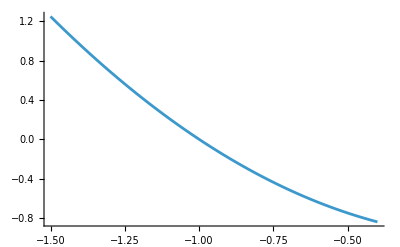

```mathematica
(* Trivial root *)
κVal=0.4;
temp=(dW/.Λcandidates[[1]])/.{κ->κVal}//Simplify;
Plot[temp,{x,-1.5,-κVal}]
```

0.0445753

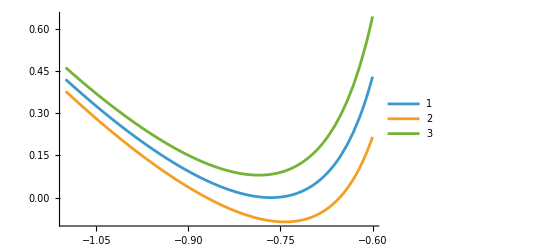

```mathematica
(* Non-trivial root that we need *)
κVal=0.4;
ΛVal=(Λ/.Λcandidates[[2]])/.{κ->κVal}//N

dW1=dW/.{κ->κVal,Λ->ΛVal};
dW2=dW/.{κ->κVal,Λ->0.8*ΛVal};
dW3=dW/.{κ->κVal,Λ->1.2*ΛVal};
Plot[{dW1,dW2,dW3},{x,-1.1,-1.5*κVal},PlotLegends->Automatic]
```

0.195425

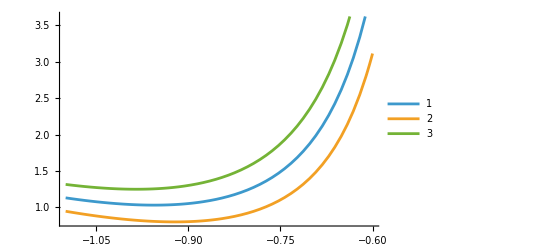

```mathematica
(* Non-trivial root that is not relevant for this vacuum (will be relevant for the other vacuum) *)
κVal=0.4;
ΛVal=(Λ/.Λcandidates[[3]])/.{κ->κVal}//N

dW1=dW/.{κ->κVal,Λ->ΛVal};
dW2=dW/.{κ->κVal,Λ->0.8*ΛVal};
dW3=dW/.{κ->κVal,Λ->1.2*ΛVal};
Plot[{dW1,dW2,dW3},{x,-1.1,-1.5*κVal},PlotLegends->Automatic]
```

```mathematica
(* End result for Λ *)
Λcrit1=Λ/.Λcandidates[[2]]
```

1/18 (2+κ^2-√3 κ √(4-κ^2))

-1+x^2+((1+3 x^2+6 x κ+2 κ^2) (2+κ^2-√3 κ √(4-κ^2)))/(18 (x+κ)^2)

{-1/(√3)-κ/2+O[κ]^(3/2),1/(√3)-(√κ)/3^(1/4)-κ/2+O[κ]^(3/2),-1/(√3)-κ/2+O[κ]^(3/2),1/(√3)+(√κ)/3^(1/4)-κ/2+O[κ]^(3/2)}

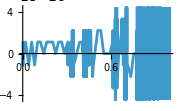

```mathematica
temp=dW/.{Λ->Λcrit1}
roots=x/.Solve[temp==0,x];
Series[roots,{κ,0,1}]
Plot[roots[[1]]-roots[[3]],{κ,0,1},ImageSize->Small]
xcrit=FullSimplify[roots[[1]],Assumptions->{0<κ<1}];
```

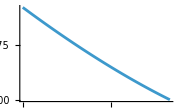

```mathematica
Plot[xcrit,{κ,0,1},ImageSize->Small]
```

```mathematica
(* End result for x *)
xrootcrit1=xcrit
```

1/12 (-6 κ-√6 (√(κ (3 κ+√3 √(4-κ^2)))+√(8+κ^2+√3 κ √(4-κ^2)-2 √2 √(-κ (-4+κ^2) (3 κ+√3 √(4-κ^2))))))

#### Method 2 : polynomial division

When a polynomial has a double root, its GCD with its derivative is non-trivial. One can do Euclidean division to fing this case.

```mathematica
PolydW=FullSimplify[(x+κ)^2*dW]
```

(-1+x^2) (x+κ)^2+(1+3 x^2+6 x κ+2 κ^2) Λ

```mathematica
(* Euclidean algorythm *)
poly1=PolydW;
poly2=D[poly1,x];
polyQuot=x;
polyRem=x^2;

While[Exponent[polyRem,x]!=0,
{temp=PolynomialQuotientRemainder[poly1,poly2,x];
polyQuot=temp[[1]];
polyRem=temp[[2]];
poly1=poly2;
poly2=polyRem;}
]

polyQuot//Simplify
polyRem//Simplify
```

((2+κ^2-6 Λ)^2 (κ^7 Λ-3 κ^5 (-1+Λ+7 Λ^2)+κ (1-3 Λ)^2 (3-46 Λ+27 Λ^2)+6 κ^3 (-1+11 Λ-47 Λ^2+69 Λ^3)+x (-κ^6 (-1+Λ)+6 κ^4 (1-4 Λ) Λ+2 (1-3 Λ)^2 (1-10 Λ+9 Λ^2)+3 κ^2 (-1+9 Λ-35 Λ^2+51 Λ^3))))/(32 (-1+κ^4 (-1+Λ)+13 Λ-39 Λ^2+27 Λ^3+2 κ^2 (1-7 Λ+15 Λ^2))^2)

-((-1+κ^2) (2+κ^2-6 Λ)^2 Λ (κ^6 (-1+2 Λ)+κ^4 (3+3 Λ-17 Λ^2)+(1-10 Λ+9 Λ^2)^2+κ^2 (-3+15 Λ-101 Λ^2+153 Λ^3)))/(4 (-1+κ^4 (-1+Λ)+13 Λ-39 Λ^2+27 Λ^3+2 κ^2 (1-7 Λ+15 Λ^2))^2)

```mathematica
Λcandidates=Simplify[Λ/.Solve[polyRem==0,Λ],Assumptions->{0<κ<1}]
```

{0,1/6 (2+κ^2),1/6 (2+κ^2),1/18 (2+κ^2-√3 κ √(4-κ^2)),1/18 (2+κ^2+√3 κ √(4-κ^2)),1-κ^2-κ √(-1+κ^2),1-κ^2+κ √(-1+κ^2)}

The root Λ=0 is trivial, two roots lead to unphysial x, two roots are imaginary for 0<κ<1. From the two roots left we pick the smallest one.

```mathematica
(*Λcandidates//InputForm
Λcandidates={{Λ->0},{Λ->(2+κ^2-Sqrt[3]*κ*Sqrt[4-κ^2])/18},{Λ->(2+κ^2+Sqrt[3]*κ*Sqrt[4-κ^2])/18},{Λ->1-κ^2-κ*Sqrt[-1+κ^2]},{Λ->1-κ^2+κ*Sqrt[-1+κ^2]}}*)
```

```mathematica
(* End result for Λ *)
Λcrit2=Λcandidates[[4]]
```

1/18 (2+κ^2-√3 κ √(4-κ^2))

```mathematica
(* Euclidean algorythm again, to determine the quotient *)
poly1=PolydW;
poly2=D[poly1,x];
polyQuot=x;
polyRem=x^2;

While[Exponent[polyRem,x]>1,
{temp=PolynomialQuotientRemainder[poly1,poly2,x];
polyQuot=temp[[1]];
polyRem=temp[[2]];
poly1=poly2;
poly2=polyRem;}
]

xrootcrit=x/.Solve[polyRem==0,x][[1]]//Simplify;

(* End result for x *)
xrootcrit2=xrootcrit/.{Λ->Λcrit2}//Simplify
```

(2 (-1+κ^2) (-16+κ^2-4 √3 κ √(4-κ^2)))/(9 κ^3-16 √3 √(4-κ^2)+13 √3 κ^2 √(4-κ^2))

#### Compare the two methods and save results

```mathematica
Print["Next output should be zero (Λcrit from two methods):"]
Λcrit1-Λcrit2//Simplify
```

Next output should be zero (Λcrit from two methods):

0

1/12 (-6 κ-√6 (√(κ (3 κ+√3 √(4-κ^2)))+√(8+κ^2+√3 κ √(4-κ^2)-2 √2 √(-κ (-4+κ^2) (3 κ+√3 √(4-κ^2))))))

(2 (-1+κ^2) (-16+κ^2-4 √3 κ √(4-κ^2)))/(9 κ^3-16 √3 √(4-κ^2)+13 √3 κ^2 √(4-κ^2))

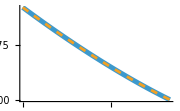

```mathematica
xrootcrit1
xrootcrit2
Plot[{xrootcrit1,xrootcrit2},{κ,0,1},PlotStyle->{{Thickness[0.02]},{Dashed}},PlotLegends->Automatic,ImageSize->Small]
```

```mathematica
(* Get λ *)
λcrit=λSubstΛ/.{Λ->Λcrit1}//FullSimplify
λcrit/.{κ->0}
λcrit/.{κ->1}
```

1/3 m √(π/2) √(2+κ^2-√3 κ √(4-κ^2))

(m √π)/3

0

```mathematica
Getκcrit[λcritVal_]:=Module[{},
κ/.FindRoot[λcrit/m==λcritVal,{κ,0.5}]
]
Getκcrit[0.1]
λcrit/.{κ->Getκcrit[0.1]}
```

0.849832

0.1 m

λcrit=0.374216

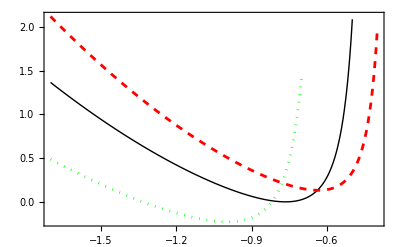

```mathematica
(* Plot dW at λ close to critical *)
mVal=1;
κVal=0.4;
λVal=λcrit/.{m->mVal,κ->κVal};
Print["λcrit=",λVal]
dWforplot=D[Wfull,X]/mVal/.{m->mVal,κ->κVal,Y->0,X->mVal/(2*λVal)*x};

xleft=-1.7;
xright=-0.5;

λVal1=0.7*λcrit/.{m->mVal,κ->κVal};
dWforplot1=dWforplot/.{λ->λVal1};
MyLineStyle1=Directive[Dotted,Green];
pLine1=Plot[dWforplot1,{x,xleft,xright},PlotStyle->MyLineStyle1];

λVal2=λcrit/.{m->mVal,κ->κVal};
dWforplot2=dWforplot/.{λ->λVal2};
MyLineStyle2=Directive[Thick,Black];
pLine2=Plot[dWforplot2,{x,xleft,xright},PlotStyle->MyLineStyle2];

λVal3=1.3*λcrit/.{m->mVal,κ->κVal};
dWforplot3=dWforplot/.{λ->λVal3};
MyLineStyle3=Directive[Dashed,Red];
pLine3=Plot[dWforplot3,{x,xleft,0.8*xright},PlotStyle->MyLineStyle3];

(*Legend:build entries correctly and place them*)
leg=Placed[Column[{
LineLegend[{MyLineStyle1},{""},LabelStyle->{Black,10},LegendMarkerSize->{25,5}],
LineLegend[{MyLineStyle2},{""},LabelStyle->{Black,10},LegendMarkerSize->{25,5}],LineLegend[{MyLineStyle3},{""},LabelStyle->{Black,10},LegendMarkerSize->{25,5}]
}],{0.55,0.75}];

(*Final figure with legend*)
MyPlot=Legended[Show[pLine1,pLine2,pLine3,Frame->True,Axes->{True,False},AxesOrigin->{-1,0},FrameLabel->{"",""},PlotRange->All,LabelStyle->{Black,13}],leg]
Export["MSTB_near_crit_dWfull.pdf",MyPlot];
```

λcrit=0.374216

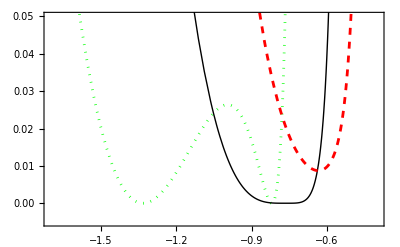

```mathematica
(* Plot potential at λ close to critical *)
mVal=1;
κVal=0.4;
λVal=λcrit/.{m->mVal,κ->κVal};
Print["λcrit=",λVal]
Vforplot=Vfull/mVal^2/.{m->mVal,κ->κVal,Y->0,X->mVal/(2*λVal)*x};

xleft=-1.7;
xright=-0.5;

λVal1=0.7*λcrit/.{m->mVal,κ->κVal};
Vforplot1=Vforplot/.{λ->λVal1};
MyLineStyle1=Directive[Dotted,Green];
pLine1=Plot[Vforplot1,{x,xleft,xright},PlotStyle->MyLineStyle1];

λVal2=λcrit/.{m->mVal,κ->κVal};
Vforplot2=Vforplot/.{λ->λVal2};
MyLineStyle2=Directive[Thick,Black];
pLine2=Plot[Vforplot2,{x,xleft,xright},PlotStyle->MyLineStyle2];

λVal3=1.3*λcrit/.{m->mVal,κ->κVal};
Vforplot3=Vforplot/.{λ->λVal3};
MyLineStyle3=Directive[Dashed,Red];
pLine3=Plot[Vforplot3,{x,xleft,0.8*xright},PlotStyle->MyLineStyle3];

(*Legend:build entries correctly and place them*)
leg=Placed[Column[{
LineLegend[{MyLineStyle1},{""},LabelStyle->{Black,10},LegendMarkerSize->{25,5}],
LineLegend[{MyLineStyle2},{""},LabelStyle->{Black,10},LegendMarkerSize->{25,5}],LineLegend[{MyLineStyle3},{""},LabelStyle->{Black,10},LegendMarkerSize->{25,5}]
}],{0.3,0.75}];

(*Final figure with legend*)
MyPlot=Legended[Show[pLine1,pLine2,pLine3,Frame->True,Axes->{True,False},AxesOrigin->{-1,0},FrameLabel->{"",""},PlotRange->{{Automatic,Automatic},{-0.005,0.05}},LabelStyle->{Black,13}],leg]
Export["MSTB_near_crit_Vfull.pdf",MyPlot];
```

### Investigating nature of vacua analytically (assuming 0<κ<1, right vacuum)

#### Simplify expression for superpotential

```mathematica
(* Rewrite dWfull/dX in a simpler form *)
mVal=1;
λSubstΛ=m*Sqrt[Pi*Λ];
(* That was for the left vacuum *)
dWleft=FullSimplify[(D[Wfull,X]*4*λ/m^2/.{Y->0,X->x*m/(2*λ)})/.{λ->λSubstΛ},Assumptions->{0<κ<1,Λ>0,κ+x<0}]
(* This is now *)
dWright=FullSimplify[(D[Wfull,X]*4*λ/m^2/.{Y->0,X->x*m/(2*λ)})/.{λ->λSubstΛ},Assumptions->{0<κ<1,Λ>0,κ+x>0}]
(* Check that these two expressions differ only by an overall sign *)
Print["Next output should be zero:"]
dWleft+dWright//Simplify
```

-1+x^2+((1+3 x^2+6 x κ+2 κ^2) Λ)/(x+κ)^2

1-x^2-((1+3 x^2+6 x κ+2 κ^2) Λ)/(x+κ)^2

Next output should be zero:

0

#### Get the first and the second critical Λ and λ

```mathematica
(* Discriminant method *)
PolydW=FullSimplify[(x+κ)^2*dWleft];
PolydWdiscr=Discriminant[PolydW,x]//Simplify;
ΛcandidatesMethod1=Simplify[Λ/.Solve[PolydWdiscr==0,Λ],Assumptions->{0<κ<1}];
```

```mathematica
(* Euclidean algorythm *)
poly1=PolydW;
poly2=D[poly1,x];
polyQuot=x;
polyRem=x^2;

While[Exponent[polyRem,x]!=0,
{temp=PolynomialQuotientRemainder[poly1,poly2,x];
polyQuot=temp[[1]];
polyRem=temp[[2]];
poly1=poly2;
poly2=polyRem;}
];

ΛcandidatesMethod2=Simplify[Λ/.Solve[polyRem==0,Λ],Assumptions->{0<κ<1}];
```

```mathematica
ΛcandidatesMethod1
ΛcandidatesMethod2
```

{0,1/18 (2+κ^2-√3 κ √(4-κ^2)),1/18 (2+κ^2+√3 κ √(4-κ^2)),1-κ^2-κ √(-1+κ^2),1-κ^2+κ √(-1+κ^2)}

{0,1/6 (2+κ^2),1/6 (2+κ^2),1/18 (2+κ^2-√3 κ √(4-κ^2)),1/18 (2+κ^2+√3 κ √(4-κ^2)),1-κ^2-κ √(-1+κ^2),1-κ^2+κ √(-1+κ^2)}

```mathematica
ΛcandidatesMethod1[[2]]//InputForm
```

(2 + κ^2 - Sqrt[3]*κ*Sqrt[4 - κ^2])/18

```mathematica
ΛcandidatesMethod1[[3]]//InputForm
```

(2 + κ^2 + Sqrt[3]*κ*Sqrt[4 - κ^2])/18

```mathematica
(* Save the first and the second critical values *)
ΛcritFirst=(2+κ^2-Sqrt[3]*κ*Sqrt[4-κ^2])/18
ΛcritSecond=(2+κ^2+Sqrt[3]*κ*Sqrt[4-κ^2])/18
```

1/18 (2+κ^2-√3 κ √(4-κ^2))

1/18 (2+κ^2+√3 κ √(4-κ^2))

```mathematica
(* Recompute into λ *)
```

```mathematica
λcritFirst=λSubstΛ/.{Λ->ΛcritFirst}
λcritSecond=λSubstΛ/.{Λ->ΛcritSecond}
```

1/3 m √(π/2) √(2+κ^2-√3 κ √(4-κ^2))

1/3 m √(π/2) √(2+κ^2+√3 κ √(4-κ^2))

0.374216

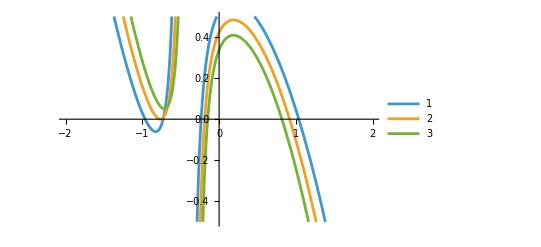

```mathematica
(* First critical point *)
mVal=1;
κVal=0.4;
λVal=λcritFirst/.{κ->κVal,m->mVal}//N

dW=D[Wfull,X]/.{κ->κVal,m->mVal,Y->0,X->x*mVal/(2*λVal)};
dW1=dW/.{λ->0.9*λVal};
dW2=dW/.{λ->1.0*λVal};
dW3=dW/.{λ->1.1*λVal};
Plot[{dW1,dW2,dW3},{x,-2,2},PlotRange->{{Automatic,Automatic},{-0.5,0.5}},PlotLegends->Automatic]
```

0.783546

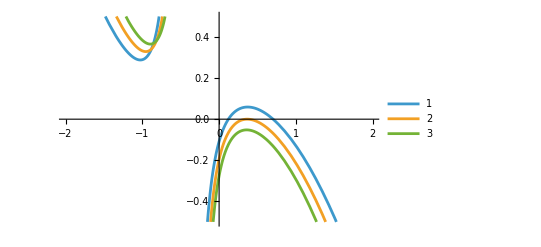

```mathematica
(* Second critical point *)
mVal=1;
κVal=0.4;
λVal=λcritSecond/.{κ->κVal,m->mVal}//N

dW=D[Wfull,X]/.{κ->κVal,m->mVal,Y->0,X->x*mVal/(2*λVal)};
dW1=dW/.{λ->0.9*λVal};
dW2=dW/.{λ->1.0*λVal};
dW3=dW/.{λ->1.1*λVal};
Plot[{dW1,dW2,dW3},{x,-2,2},PlotRange->{{Automatic,Automatic},{-0.5,0.5}},PlotLegends->Automatic]
```

```mathematica
(* End result for λ *)
λcritFirst
λcritSecond
```

1/3 m √(π/2) √(2+κ^2-√3 κ √(4-κ^2))

1/3 m √(π/2) √(2+κ^2+√3 κ √(4-κ^2))

```mathematica
(* Determine the left vacuum at the first critical point *)
λVal=λcritFirst;
dW=D[Wfull,X]/.{λ->λVal,Y->0,X->x*m/(2*λVal)}//Simplify
roots=x/.Solve[dW==0,x,Assumptions->{0<κ<1}];
Series[roots,{κ,0,1}]
```

1/(12 √(2 π) (x+κ)^3)m √((x+κ)^2/(2+κ^2-√3 κ √(4-κ^2))) (-2-18 x^4-36 x^3 κ+13 κ^2-2 κ^4+√3 κ √(4-κ^2)+2 √3 κ^3 √(4-κ^2)-6 x κ (-4+κ^2-√3 κ √(4-κ^2))+3 x^2 (4-7 κ^2+√3 κ √(4-κ^2)))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{-1/(√3)-κ/2+O[κ]^(3/2),1/(√3)-(√κ)/3^(1/4)-κ/2+O[κ]^(3/2),-1/(√3)-κ/2+O[κ]^(3/2),1/(√3)+(√κ)/3^(1/4)-κ/2+O[κ]^(3/2)}

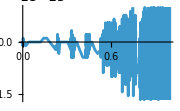

```mathematica
Plot[roots[[1]]-roots[[3]],{κ,0,1},ImageSize->Small]
xcritFirst=Simplify[roots[[1]],Assumptions->{0<κ<1}];
```

```mathematica
(* Determine the left vacuum at the second critical point *)
λVal=λcritSecond;
dW=D[Wfull,X]/.{λ->λVal,Y->0,X->x*m/(2*λVal)}//Simplify
roots=x/.Solve[dW==0,x,Assumptions->{0<κ<1}];
Series[roots,{κ,0,1}]
```

-1/(12 √(2 π) (x+κ)^3)m √((x+κ)^2/(2+κ^2+√3 κ √(4-κ^2))) (2+18 x^4+36 x^3 κ-13 κ^2+2 κ^4+√3 κ √(4-κ^2)+2 √3 κ^3 √(4-κ^2)+6 x κ (-4+κ^2+√3 κ √(4-κ^2))+3 x^2 (-4+7 κ^2+√3 κ √(4-κ^2)))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{-1/(√3)+(√κ √κ)/(3^(1/4) √-κ)-κ/2+O[κ]^(3/2),1/(√3)-κ/2+O[κ]^(3/2),-1/(√3)-(√κ √κ)/(3^(1/4) √-κ)-κ/2+O[κ]^(3/2),1/(√3)-κ/2+O[κ]^(3/2)}

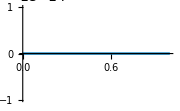

```mathematica
Plot[roots[[2]]-roots[[2]],{κ,0,1},PlotRange->{{Automatic,Automatic},{-10^(-14),10^(-14)}},ImageSize->Small]
xcritSecond=Simplify[roots[[2]],Assumptions->{0<κ<1}];
```

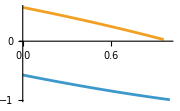

```mathematica
Plot[{xcritFirst,xcritSecond},{κ,0,1},ImageSize->Small,PlotLegends->Automatic]
```

#### Check the potential at the critical points

Make sure that it’s a minimum and not a saddle point

```mathematica
(* Bosonic fluctuation operator *)
fields={X,Y};
ddUfull=Table[Table[D[Vfull,f1,f2]//Simplify,{f1,fields}],{f2,fields}];
```

```mathematica
(* At the first critical point *)
xVal=xcritFirst;
λVal=λcritFirst;
ddUfirst=ddUfull/.{λ->λVal,X->xVal*m/(2*λVal),Y->0};
(* This expression is too complicated, let's consider some examples *)
mVal=1;
κVal=0.1;
temp=ddUfirst/.{m->mVal,κ->κVal}
```

{{1.90142×10^-15,0},{0,0.01}}

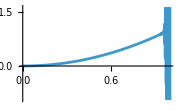

```mathematica
Plot[ddUfirst[[2]][[2]]/.{m->1},{κ,0,1},ImageSize->Small]
```

```mathematica
(* At the second critical point *)
xVal=xcritSecond;
λVal=λcritSecond;
ddUsecond=ddUfull/.{λ->λVal,X->xVal*m/(2*λVal),Y->0};
(* This expression is too complicated, let's consider some examples *)
mVal=1;
κVal=0.6;
temp=ddUsecond/.{m->mVal,κ->κVal}
```

{{1.63956×10^-16+1.67496×10^-31 ⅈ,0},{0,0.36+4.69794×10^-17 ⅈ}}

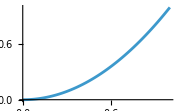

```mathematica
Plot[ddUsecond[[2]][[2]]/.{m->1},{κ,0,1},ImageSize->Small]
```

#### Save results

```mathematica
(* End result for λ *)
λcritFirst
λcritSecond
```

1/3 m √(π/2) √(2+κ^2-√3 κ √(4-κ^2))

1/3 m √(π/2) √(2+κ^2+√3 κ √(4-κ^2))

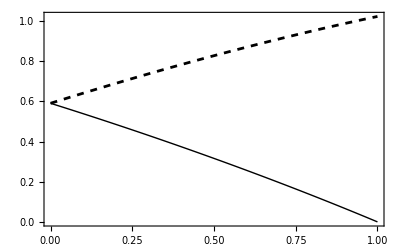

```mathematica
(* Plot λcrit *)
MyLineStyle1=Directive[Thick,Black];
pLine1=Plot[λcritFirst/m,{κ,0,1},PlotStyle->MyLineStyle1];

MyLineStyle2=Directive[Dashed,Black];
pLine2=Plot[λcritSecond/m,{κ,0,1},PlotStyle->MyLineStyle2];

(*Legend:build entries correctly and place them*)
leg=Placed[Column[{
LineLegend[{MyLineStyle1},{""},LabelStyle->{Black,10},LegendMarkerSize->{25,5}],
LineLegend[{MyLineStyle2},{""},LabelStyle->{Black,10},LegendMarkerSize->{25,5}]
}],{0.85,0.55}];

(*Final figure with legend*)
MyPlot=Legended[Show[pLine1,pLine2,Frame->True,FrameLabel->{"",""},PlotRange->All,LabelStyle->{Black,13}],leg]

Export["MSTB_lambda_crit_2.pdf",MyPlot];
```

```mathematica
(* End result for x *)
xcritFirst;
xcritSecond;
```

```mathematica
GetκcritFirst[λcritVal_]:=Module[{},
κ/.FindRoot[λcritFirst/m==λcritVal,{κ,0.5}]
]
GetκcritFirst[0.1]
λcritFirst/.{κ->GetκcritFirst[0.1]}

GetκcritSecond[λcritVal_]:=Module[{},
κ/.FindRoot[λcritSecond/m==λcritVal,{κ,0.5}]
]
GetκcritSecond[0.9]
λcritSecond/.{κ->GetκcritSecond[0.9]}
```

0.849832

0.1 m

0.671245

0.9 m

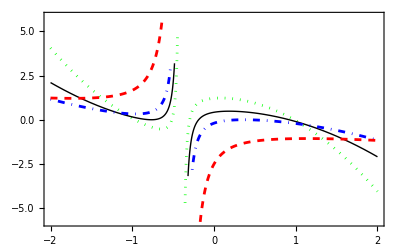

```mathematica
(* Plot dW at λ close to critical *)
mVal=1;
κVal=0.4;
dWforplot=D[Wfull,X]/mVal/.{m->mVal,κ->κVal,Y->0};

xleft=-2;
xright=2;

λVal=0.5*λcritFirst/.{m->mVal,κ->κVal};
dWforplot1=dWforplot/.{λ->λVal,X->mVal/(2*λVal)*x};
MyLineStyle1=Directive[Dotted,Green];
pLine1=Plot[dWforplot1,{x,xleft,xright},PlotStyle->MyLineStyle1];

λVal=λcritFirst/.{m->mVal,κ->κVal};
dWforplot2=dWforplot/.{λ->λVal,X->mVal/(2*λVal)*x};
MyLineStyle2=Directive[Thick,Black];
pLine2=Plot[dWforplot2,{x,xleft,xright},PlotStyle->MyLineStyle2];

λVal=λcritSecond/.{m->mVal,κ->κVal};
dWforplot3=dWforplot/.{λ->λVal,X->mVal/(2*λVal)*x};
MyLineStyle3=Directive[DotDashed,Blue];
pLine3=Plot[dWforplot3,{x,xleft,xright},PlotStyle->MyLineStyle3];

λVal=5*λcritSecond/.{m->mVal,κ->κVal};
dWforplot4=dWforplot/.{λ->λVal,X->mVal/(2*λVal)*x};
MyLineStyle4=Directive[Dashed,Red];
pLine4=Plot[dWforplot4,{x,xleft,xright},PlotStyle->MyLineStyle4];

(*Legend:build entries correctly and place them*)
leg=Placed[Column[{
LineLegend[{MyLineStyle1},{""},LabelStyle->{Black,10},LegendMarkerSize->{25,5}],
LineLegend[{MyLineStyle2},{""},LabelStyle->{Black,10},LegendMarkerSize->{25,5}],LineLegend[{MyLineStyle3},{""},LabelStyle->{Black,10},LegendMarkerSize->{25,5}],LineLegend[{MyLineStyle4},{""},LabelStyle->{Black,10},LegendMarkerSize->{25,5}]
}],{0.85,0.75}];

(*Final figure with legend*)
MyPlot=Legended[Show[pLine1,pLine2,pLine3,pLine4,Frame->True,Axes->{True,False},AxesOrigin->{-1,0},FrameLabel->{"",""},PlotRange->All,LabelStyle->{Black,13}],leg]
```

### Correction to kink mass - exact numerical

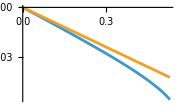

```mathematica
mVal=1;
Wnum=Simplify[Wfull/.{m->mVal,Y->0},Assumptions->{0<κ<1}];
dWnumdX=Simplify[D[Wfull,X]/.{m->mVal,Y->0},Assumptions->{0<κ<1}];

KinkMassQuant[κVal_,λVal_]:=Module[{w,X1,X2,dW,roots,ans},
dW=dWnumdX/.{κ->κVal,λ->λVal};
roots=X/.NSolve[dW==0,X,Reals];
X1=Max[roots];
X2=Min[roots];
w=Wnum/.{κ->κVal,λ->λVal};
ans=(w/.{X->X1})-(w/.{X->X2})
]

dKinkMassQuant[κVal_,λVal_]:=Module[{ans},
ans=KinkMassQuant[κVal,λVal]-KinkMassClass[κVal,λVal]
]

KinkMassClass[κVal_,λVal_]:=Module[{ans},
ans=mVal^3/(12*λVal^2)*κVal*(3-κVal^2)
]

dKinkMass1loop[κVal_]:=Module[{ans},
ans=ΔE/.{m->mVal,κ->κVal}
]


λVal=0.3;
κMax=Getκcrit[λVal];
Plot[{dKinkMassQuant[κ,λVal],dKinkMass1loop[κ]},{κ,0,κMax},PlotLegends->Automatic,PlotRange->All,ImageSize->Small]
```

### Bosonic quantum corrections from hep-th/0205137

#### Correction to the sphaleron mass

```mathematica
dMsphQuant=-m/(Pi*Sqrt[2])*((3-Pi/Sqrt[12])+(1-Sqrt[κ^2-1])*ArcSin[1/κ])
```

-(m (3-π/(2 √3)+(1-√(-1+κ^2)) ArcSin[1/κ]))/(√2 π)

```mathematica
dMser=Series[dMsphQuant,{κ,0,0}]
dMser=dMser//Normal//ComplexExpand;
Simplify[Re[dMser]//ComplexExpand,Assumptions->{κ>0}]
Simplify[Im[dMser]//ComplexExpand,Assumptions->{κ>0}]
```

(m (-18+√3 π+(3-3 ⅈ) √(-1/κ^2) κ Log[-4/κ^2]))/(6 √2 π)+O[κ]^1

(m (-18+(-3+√3) π+Log[64]-6 Log[κ]))/(6 √2 π)

(m (π+Log[4]-2 Log[κ]))/(2 √2 π)

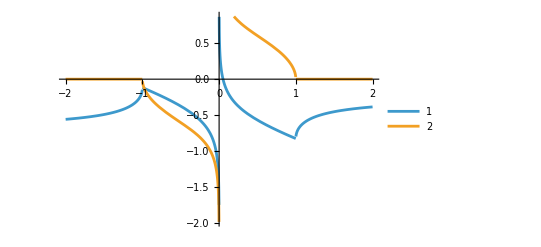

```mathematica
RedM=Re[dMsphQuant/.{m->1}];
ImdM=Im[dMsphQuant/.{m->1}];
Plot[{RedM,ImdM},{κ,-2,2},PlotLegends->Automatic]
```

#### Correction to the kink mass - comparing to SUSY

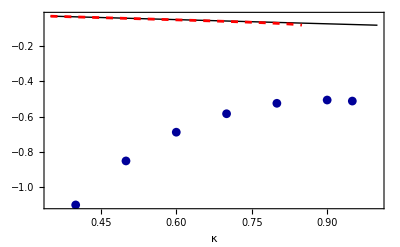

```mathematica
mVal=1;
κMin=0.35;

(* Quantum correction exact 1 *)
λVal1=0.1;
κMax1=Getκcrit[λVal1];
MyLineStyle1=Directive[Dashed,Red];
pLine1=Plot[dKinkMassQuant[κ,λVal1],{κ,κMin,κMax1},PlotStyle->MyLineStyle1];

(* Quantum correction approx *)
Δsusy1loop=ΔE/.{m->mVal};
κMax3=1;
MyLineStyle3=Directive[Thick,Black];
pLine3=Plot[Δsusy1loop,{κ,κMin,κMax3},PlotStyle->MyLineStyle3];

(* Corrections from that paper *)
Δbos={
{0.4,−1.103270},
{0.5,−0.852622},
{0.6,−0.689001},
{0.7,−0.583835},
{0.8,−0.524363},
{0.9,−0.505708},
{0.95,−0.511638}
};
MyDotStyle=Directive[Darker[Blue,.4]];
pPts=ListPlot[Δbos,PlotStyle->MyDotStyle,PlotMarkers->{"●",9}];

(*Legend:build entries correctly and place them*)
leg=Placed[Column[{
LineLegend[{MyLineStyle1},{"SUSY exact"},LabelStyle->{Black,10},LegendMarkerSize->{25,5}],
LineLegend[{MyLineStyle3},{"SUSY lead"},LabelStyle->{Black,10},LegendMarkerSize->{25,5}],PointLegend[{MyDotStyle},{"Bos 1-loop"},LegendMarkers->{{"●",8}},LabelStyle->{Black,10},LegendMarkerSize->{25,8}]}],
{0.8,0.2}];

(*Final figure with legend*)
MyPlot=Legended[Show[pLine3,pLine1,pPts,Frame->True,FrameLabel->{"κ",""},PlotRange->All],leg]
Export["MSTB_kink_mass_quantum_correction.pdf",MyPlot];
```

## Supplementary computations

### Check of the action on the degenerate kinks for 0<κ<1

```mathematica
XtrajKink
YtrajKink
KinkSub
```

(m Tanh[(m z κ)/2])/(2 λ)

(m √(1-κ^2))/(2 λ Cosh[(m z κ)/2])

{X→(m Tanh[(m z κ)/2])/(2 λ),Y→(m √(1-κ^2))/(2 λ Cosh[(m z κ)/2])}

```mathematica
(* Eq. (3.11) *)
dX2=D[XtrajKink,z]^2;
dY2=D[YtrajKink,z]^2;
SkinkIntegrand=dX2/2+dY2/2+(V/.KinkSub)//Simplify
Skink=Integrate[SkinkIntegrand,{z,-Infinity,Infinity},Assumptions->{m>0,0<κ<1,λ>0}]
```

-(m^4 κ^2 (-1-κ^2+(-1+κ^2) Cosh[m z κ]))/(32 λ^2 Cosh[(m z κ)/2]^4)

-(m^3 κ (-3+κ^2))/(12 λ^2)

```mathematica
Print["The following output should be zero (kink energy via two methods):"]
Ekink-Skink//Simplify
```

The following output should be zero (kink energy via two methods):

0

### Check of the action on the sphaleron

```mathematica
XtrajSphaleron
YtrajSphaleron
SubSph
```

(m Tanh[(m z)/2])/(2 λ)

0

{X→(m Tanh[(m z)/2])/(2 λ),Y→0}

```mathematica
(* Eq. (3.11) *)
dX2=D[XtrajSphaleron,z]^2;
dY2=D[YtrajSphaleron,z]^2;
SsphIntegrand=dX2/2+dY2/2+(V/.SubSph)//Simplify
Ssph=Integrate[SsphIntegrand,{z,-Infinity,Infinity},Assumptions->{m>0,0<κ<1,λ>0}]
```

m^4/(16 λ^2 Cosh[(m z)/2]^4)

m^3/(6 λ^2)

```mathematica
Print["The following output should be zero (sphaleron energy via two methods):"]
Esph-Ssph//Simplify
```

The following output should be zero (sphaleron energy via two methods):

0

### Kink action in a ϕ^4 model with generic coefficients (used in Sec. 3.6.1)

```mathematica
(* Define the energy functional *)
ϕ4potential=μ^4/(4*Λ)-μ^2/2*ϕ[t]^2+Λ/4*ϕ[t]^4
ϕ4kinetic=η*D[ϕ[t],t]^2/2
ϕ4action=ϕ4kinetic+ϕ4potential;
```

μ^4/(4 Λ)-1/2 μ^2 ϕ[t]^2+1/4 Λ ϕ[t]^4

1/2 η ϕ'[t]^2

```mathematica
(* Check potential *)
ϕ4action/.{ϕ->Function[t,μ/Sqrt[Λ]]}//Simplify
```

0

```mathematica
(* Build equations of motion *)
ϕ4EOM=D[D[ϕ4action,Derivative[1][ϕ][t]],t]-D[ϕ4action,ϕ[t]]

(* Check kink solution *)
ϕ4kink[t_]:=μ/Sqrt[Λ]*Tanh[t*μ/Sqrt[2*η]]
Print["The following output should be zero (EOM):"]
ϕ4EOM/.{ϕ->Function[t,ϕ4kink[t]]}//Simplify
```

μ^2 ϕ[t]-Λ ϕ[t]^3+η ϕ''[t]

The following output should be zero (EOM):

0

```mathematica
(* Compute kink action by direct integration *)
ϕ4integrand=ϕ4action/.{ϕ->Function[t,ϕ4kink[t]]}//Simplify
ϕ4action=Integrate[ϕ4integrand,{t,-Infinity,Infinity},Assumptions->{μ>0,Λ>0,η>0}]
```

μ^4/(2 Λ Cosh[(t μ)/(√2 √η)]^4)

ConditionalExpression[(2 √2 √η μ^3)/(3 Λ), ]